```mathematica
Select[DictionaryLookup[],EditDistance["sophia",#]<3&]//FullForm;
```

```mathematica
languageList=DictionaryLookup[All]
```

{Arabic,BrazilianPortuguese,Breton,BritishEnglish,Catalan,Croatian,Danish,Dutch,English,Esperanto,Faroese,Finnish,French,Galician,German,Hebrew,Hindi,Hungarian,IrishGaelic,Italian,Latin,Polish,Portuguese,Russian,ScottishGaelic,Spanish,Swedish}

```mathematica
convertionRule=Thread[ToUpperCase[Alphabet[]]->Range[Length[Alphabet[]]]];
```

```mathematica
normalizeToOne[listToNormalize_]:=listToNormalize / Max[listToNormalize];
```

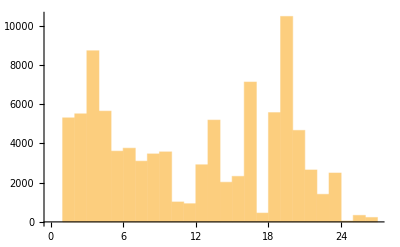

```mathematica
Histogram[ToUpperCase[StringTake[DictionaryLookup[{"English",All}],1]]/.convertionRule]
```

```mathematica
Length[DictionaryLookup[All]]
```

27

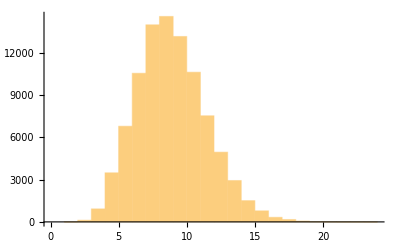

```mathematica
Histogram[Map[StringLength,DictionaryLookup[{"English",All}]]]
```

```mathematica
langAssoc=With[{langList=DictionaryLookup[All][[;;10]]},
AssociationThread[
langList,
Map[
Map[
StringLength,
DictionaryLookup[
{#,All}
]
]&,
langList
]]]
```

<|1|>
 |  |  |  |

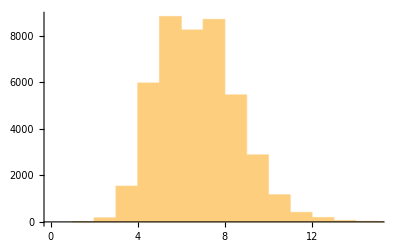
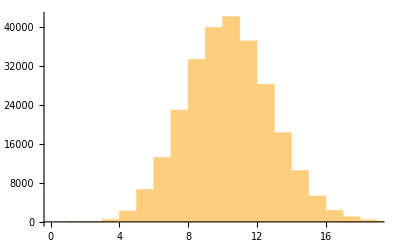
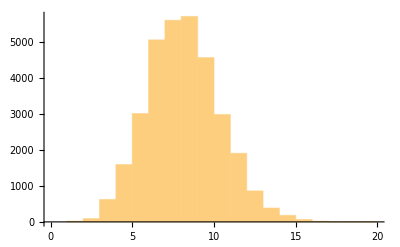
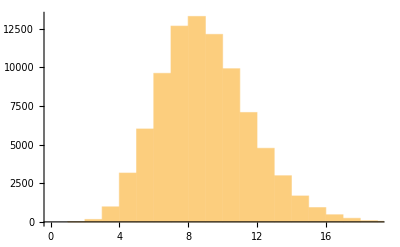
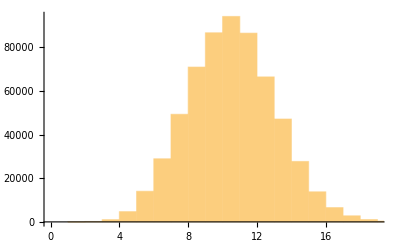
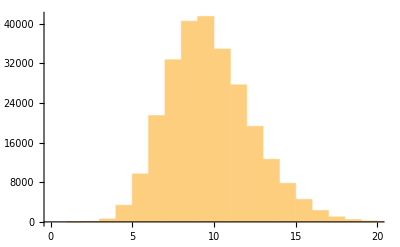
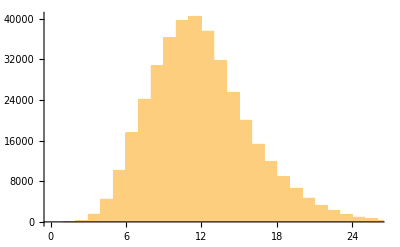
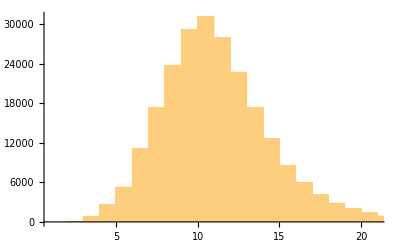
{-Graphics-Arabic,-Graphics-BrazilianPortuguese,-Graphics-Breton,-Graphics-BritishEnglish,-Graphics-Catalan,-Graphics-Croatian,-Graphics-Danish,-Graphics-Dutch,-Graphics-English,-Graphics-Esperanto}

```mathematica
(Labeled[Histogram[langAssoc[#]],#]&)/@Take[languageList,10]
```

```mathematica
List[Labeled[Histogram[langAssoc["BritishEnglish"]],"BritishEnglish"],Labeled[Histogram[langAssoc["English"]],"English"]]
```

{-Graphics-BritishEnglish,-Graphics-English}